Heat Transfer and Temperature Distribution in a Fin

```mathematica
Manipulate[
Module[{h,k, tempInf, tempBase, len,ac,p,m,tAdiabatic,qAdiabatic,tConvection,qConvection,Trev,col,table,p1,p2,p3},
h=50; (*W/m2/K*)
k=Switch[material,1,400,2,70,3,54]; (*W/m/K*)

tempInf=25; (*C*)
tempBase=100; (*C*)

len=length/100; (*centimeters to meters*)
ac=Switch[crosssection,1,t*w/1000000,2,(Pi*d^2)/4/1000000];
p=Switch[crosssection,1,2*(t+w)/1000,2,d*Pi/1000];
m=√((h*p)/(k*ac));

tAdiabatic[xa_]:=Cosh[m*(len-xa)]/Cosh[m*len]*(tempBase-tempInf)+tempInf;
qAdiabatic=√(h*p*k*ac)*(tempBase-tempInf)*Tanh[m*len];

tConvection[xa_] := (Cosh[m*(len-xa)]+(h/(m*k))*Sinh[m*(len-xa)])/(Cosh[m*len]+h/(m*k)*Sinh[m*len])*(tempBase-tempInf)+tempInf;
qConvection =√(h*p*k*ac)*(tempBase-tempInf)*(Sinh[m*len]+h/(m*k)*Cosh[m*len])/(Cosh[m*len]+h/(m*k)*Sinh[m*len]);

table=Graphics[{
Text@Style[Column[{"total heat transfer",
Framed@Column[
Row@{#1,Style[" q",Italic]," = ",NumberForm[N@#2,3]," W"}&@@@{{"adiabatic",qAdiabatic},{"convection",qConvection}},
Alignment->"="]
},Center],17]
}];

p1=Plot[{tAdiabatic[x/100],tConvection[x/100]},{x,0,length}, PlotStyle->{{Thick,RGBColor[0,0.6,0]},{Thick, Blue}},PlotRange->{{0,length},{tConvection[len],100}},
Frame->True,FrameLabel->{"distance from base (cm)","temperature (°C)"},LabelStyle->{17,Black},ImagePadding->{{80,10},{50,5}},PlotRangePadding->{{None,0.22*length},{Scaled@0.13,None}},ImageSize->{600,375},AspectRatio->Full,
Epilog->{
Inset[table,Scaled@{0.8,0.85}],
Text[Style[#1,18,#2],{length,#3},{-1.2,0}]&@@@{{"adiabatic",RGBColor[0,0.6,0],tAdiabatic[len]},{"convection",Blue,tConvection[len]}},
{Thick,Arrow[{{0,1.05*tConvection[len]-5},{length,1.05*tConvection[len]-5}}]},
Text[Style[Row@{"fin ",#1},18],{#2,1.05*tConvection[len]-5},{#3,1.5}]&@@@{{"base",0,-1.2},{"tip",length,0}}
}];

col[xa_]:=ColorData["TemperatureMap"][Rescale[tConvection[xa/100],{tempInf,tempBase}]];

p2=Show[
Graphics3D[{col[0],Cuboid[{0,-5,-40},{If[crosssection==1,w,50],0,40}]}],
If[crosssection==1,
RegionPlot3D[z<t,{x,0,w},{y,0,10*length},{z,-t/2,t/2},Mesh->None,ColorFunction->(col[#2/10]&),ColorFunctionScaling->False],
ParametricPlot3D[{d/2*Sin[θ]+25,x,d/2*Cos[θ]},{θ,0,2*π},{x,0,10*length},Mesh->None,ColorFunction->(col[#2/10]&),ColorFunctionScaling->False]
],Boxed->False,Axes->False,ViewPoint->{2,2,1},Lighting->"Neutral",PlotRange->{{0,50},{-5,200},{-40,40}},ImageSize->{600,260}(*,AspectRatio->Full*)];

(*Trev[T_]:=3.674*ArcCosh[2.051*^-26 (-2.3285*^29+9.314*^27*T+√(5.4182*^58-4.337*^57*T+8.6745*^55*T^2))];*)
(*Trev=Quiet@Interpolation[{100-#,Trev[#]}&/@Range[25,100],InterpolationOrder->1];*)

Trev=Quiet@Interpolation[{{99.,24.060000000000002},{98.,26.86},{97.,28.400000000000002},{96.,29.47},{95.,30.29},{94.,30.970000000000002},{93.,31.53},{92.,32.03},{91.,32.46},{90.,32.85},{89.,33.2},{88.,33.52},{87.,33.81},{86.,34.09},{85.,34.34},{84.,34.58},{83.,34.800000000000004},{82.,35.01},{81.,35.21},{80.,35.4},{79.,35.58},{78.,35.75},{77.,35.910000000000004},{76.,36.07},{75.,36.22},{74.,36.36},{73.,36.5},{72.,36.63},{71.,36.76},{70.,36.89},{69.,37.01},{68.,37.12},{67.,37.24},{66.,37.35},{65.,37.45},{64.,37.56},{63.,37.660000000000004},{62.,37.75},{61.,37.85},{60.,37.94},{59.,38.03},{58.,38.12},{57.,38.21},{56.,38.29},{55.,38.38},{54.,38.46},{53.,38.54},{52.,38.61},{51.,38.69},{50.,38.76},{49.,38.84},{48.,38.910000000000004},{47.,38.980000000000004},{46.,39.050000000000004},{45.,39.11},{44.,39.18},{43.,39.24},{42.,39.31},{41.,39.37},{40.,39.43},{39.,39.49},{38.,39.550000000000004},{37.,39.61},{36.,39.67},{35.,39.730000000000004},{34.,39.78},{33.,39.84},{32.,39.89},{31.,39.95},{30.,40.},{29.,40.050000000000004},{28.,40.1},{27.,40.15},{26.,40.2},{25.,40.25}},InterpolationOrder->1];

p3=DensityPlot[Trev[T],{T,25,99},{y,0,1},ColorFunction->(*"TemperatureMap",*)ColorData[{"TemperatureMap","Reverse"}],PlotPoints->50,PlotRange->{{25,100},{0,1.75}},
Frame->{{False,False},{True,False}},FrameLabel->{"temperature (°C)",None},FrameTicksStyle->Black,LabelStyle->{17,Black},ImageSize->{600,110},AspectRatio->Full,
Epilog->{
Line[{{tConvection[len],0},{tConvection[len],1.25}}],
Text[Style[NumberForm[N@tConvection[len],{5,0}],17],{tConvection[len],1.25},{0,-1.1}]
}];

Switch[display,1,p1,2,Column[{p2,p3},Center]]
],
Grid[{
{Control[{{crosssection,1,"cross section"},{1->" rectangular ",2->" pin "},Setter}],
Control[{{length,20,"fin length (cm)"} ,0.5,20,0.5 ,Appearance->"Labeled" }]},
{Control[{{material,2,"fin material"},{1->" copper ",2->" platinum ",3->" carbon steel "},Setter}],
PaneSelector[{
1->Control[{{w,5,"width (mm)"} ,5,50 ,0.5,Appearance->"Labeled"  }],
2->Control[{{d,5,"diameter (mm)"} ,5,50,0.5,Appearance->"Labeled"  }]
},Dynamic@crosssection]},
{Control[{{display,2,"display"},{1->" graph ",2->" fin "},Setter}],
PaneSelector[{1->Control[{{t,5,"height (mm)"} ,5,50, 0.5,Appearance->"Labeled"}]},Dynamic@crosssection]}
},Alignment->Left]
]
```

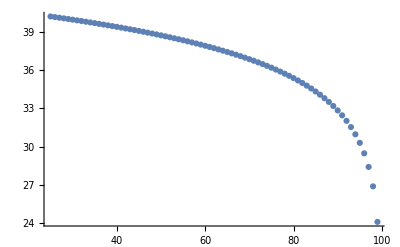

```mathematica
Module[{Trev,x,y,newT},
Trev[T_]:=3.674*ArcCosh[2.051*^-26 (-2.3285*^29+9.314*^27*T+√(5.4182*^58-4.337*^57*T+8.6745*^55*T^2))];

x=Range[100,25,-1];
y=Trev[#]&/@Range[25,100,1];

newT={x[[#]],y[[#]]}&/@Range[2,Length@x];
Round[newT,0.01];
ListPlot@newT
]
```

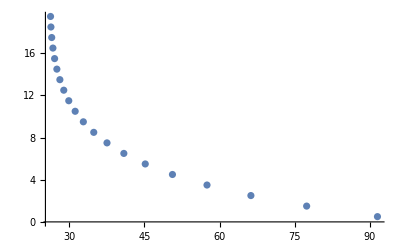

```mathematica
Module[{T,Trev},
T[x_]:=25+(75 (Cosh[20 √(10/7) (1/5-x/100)]+Sinh[20 √(10/7) (1/5-x/100)]/(4 √70)))/(Cosh[4 √(10/7)]+Sinh[4 √(10/7)]/(4 √70));
Trev[xT_]:=3.674*ArcCosh[2.051*^-26 (-2.3285*^29+9.314*^27*xT+√(5.4182*^58-4.337*^57*xT+8.6745*^55*xT^2))];

Show[
(*Plot[T[x],{x,0.5,20}],*)
ListPlot[{T[#],#}&/@Range[0.5,20]]
]
]
```

This Demonstration calculates temperature distributions and heat transfer for a fin (a.k.a. extended surface) of uniform cross-sectional area. Two possible tip conditions are considered: (1) there is no heat transfer through the tip surface (adiabatic case); (2) the tip loses heat through convection, implying that the size of the tip surface is large enough for heat loss to be taken into account. The fin is attached to a base of equal cross-sectional area that is at a constant temperature of 100 °C.  Down the length of the fin, heat is lost through natural convection to the ambient air. The temperature decreases down the fin due to conduction down the fin and to heat being lost by convection. The conduction is assumed to be one-dimensional along the length of the fin. Maximum heat transfer is achieved when the temperature of the fin is uniform, and heat is also lost through the tip. You can vary the dimensions and shape of the fin, as well as the thermal conductivity. A three-dimensional representation of the fin is also shown.

Heat Transfer Constants

tempBase = 100 °C, temperature of the base

tempInf = 100 °C, temperature of the ambient air

h=50 W/(m^2 K), convection heat transfer coefficient

k_copper=400 W/(m K) , thermal conductivity of copper

k_platinum=70 W/(m K) , thermal conductivity of platinum

k_(carbon steel)=54 W/(m K) , thermal conductivity of carbon steel

Fin Dimensions

P=perimeter (m)=2 (width+height) or π×diameter

Ac = cross sectional area (m) = width×height or π diameter^2/4

len, fin length (m)

x, position down the fin (m)

Axial Temperature Distribution

T_adiabatic=cosh[√((h P)/(k Ac))(len-x)]/cosh[√((h P)/(k Ac))len] (tempBase-tempInf)+tempInf.

T_convection = (cosh[√((h P)/(k Ac))(len-x)]+(h/(√((h P)/(k Ac))k)) sinh[√((h P)/(k Ac))(len-x)])/(cosh[√((h P)/(k Ac))len]+h/(√((h P)/(k Ac))k) sinh[√((h P)/(k Ac))len]) (tempBase-tempInf)+tempInf.

Total Heat Transfer

q_adiabatic=√(h P k Ac) (tempBase-tempInf) tanh[√((h P)/(k Ac))len].

q_convection = √(h P k Ac) (tempBase-tempInf) (sinh[√((h P)/(k Ac))len]+h/(√((h P)/(k Ac))k) cosh[√((h P)/(k Ac))len])/(cosh[√((h P)/(k Ac))len]+h/(√((h P)/(k Ac))k) sinh[√((h P)/(k Ac)) len]).

Resize Images

Rotate and Zoom in 3D

Drag Locators

Create and Delete Locators

Slider Zoom

Gamepad Controls

Automatic Animation

Bookmark Animation

fin

extended surface

heat transfer

chemical engineering

convection

conduction

Contributed by: Benjamin L. Kee

(University of Colorado Boulder, Department of Chemical and Biological Engineering)